Visualizations of qubit driving beyond the RWA

## Original Hamiltonian & Magnus effective Hamiltonians

Define original Hamiltonian in the rotating frame

```mathematica
Horig:=H1/4*(Cos[phi]*sx+Cos[2*ww*t+phi]sx+Sin[phi]sy-Sin[2*ww*t+phi]*sy)+Delta/2*sz
```

Define Magnus approximation Hamiltonians

```mathematica
gtermHww0=1/4 (2 Delta sz+H1 sx Cos[phi]+H1 sy Sin[phi]);
gtermHwwM1=1/(32 ww)(H1^2 sz-2 H1^2 sz Cos[2 (phi+α0)]+4 (Delta H1 sx+H1D sy) Cos[phi+2 α0]+4 (H1D sx-Delta H1 sy) Sin[phi+2 α0]);
gtermHwwM2=1/(256 ww^2)(-8 Delta H1^2 sz-2 H1^3 sx Cos[phi]+8 Delta H1^2 sz Cos[2 (phi+α0)]-16 Delta^2 H1 sx Cos[phi+2 α0]+16 H1DD sx Cos[phi+2 α0]-32 Delta H1D sy Cos[phi+2 α0]+2 H1^3 sx Cos[3 phi+2 α0]-H1^3 sx Cos[3 phi+4 α0]-2 H1^3 sy Sin[phi]+24 H1 H1D sz Sin[2 (phi+α0)]-32 Delta H1D sx Sin[phi+2 α0]+16 Delta^2 H1 sy Sin[phi+2 α0]-16 H1DD sy Sin[phi+2 α0]+2 H1^3 sy Sin[3 phi+2 α0]+H1^3 sy Sin[3 phi+4 α0]);
```

```mathematica
termHww0=gtermHww0/.{Delta->0,phi->0}
termHwwM1=gtermHwwM1/.{Delta->0,phi->0}//FullSimplify
uglyHeff=1/4 sx H1+(H1D sy Cos[2 α0]+H1D sx Sin[2α0])/(8 ww);
termHwwM2=gtermHwwM2/.{Delta->0,phi->0}//FullSimplify

ApproxHList=Join[Accumulate[{termHww0,termHwwM1}],{uglyHeff}]
```

(H1 sx)/4

(H1^2 sz+(4 H1D sy-2 H1^2 sz) Cos[2 α0]+4 H1D sx Sin[2 α0])/(32 ww)

(-2 H1^3 sx+2 (H1^3+8 H1DD) sx Cos[2 α0]-H1^3 sx Cos[4 α0]+2 (H1^3 sy-8 H1DD sy+12 H1 H1D sz) Sin[2 α0]+H1^3 sy Sin[4 α0])/(256 ww^2)

{(H1 sx)/4,(H1 sx)/4+(H1^2 sz+(4 H1D sy-2 H1^2 sz) Cos[2 α0]+4 H1D sx Sin[2 α0])/(32 ww),(H1 sx)/4+(H1D sy Cos[2 α0]+H1D sx Sin[2 α0])/(8 ww)}

```mathematica
gtermHwwM1/.{phi->0,Delta->0}
```

(H1^2 sz+4 H1D sy Cos[2 α0]-2 H1^2 sz Cos[2 α0]+4 H1D sx Sin[2 α0])/(32 ww)

## Definition of the driving envelopes

All jump operators are defined from the real Hamiltonian to the effective Hamiltonian

```mathematica
id2=IdentityMatrix[2];
ones2=ConstantArray[1,{2,2}];

constantH1p=Function[t,1];
(*constantJmp=Accumulate[{
0,
-1/(4ww) ⅈ H1 Sin[α0] (sx Cos[phi+α0]-sy Sin[phi+α0]),
+1/(32 ww^2) ⅈ H1 Sin[α0] (H1 sz Cos[α0]+4 Delta sx Cos[phi+α0]-2 H1 sz Cos[2 phi+α0]-4 Delta sy Sin[phi+α0])
}];*)

constantJmp=Accumulate[{
0,
1/(4ww) ⅈ (HA-HB) Sin[α0-αj] (sx Cos[phi+α0+αj]-sy Sin[phi+α0+αj]),
-1/(32 ww^2) ⅈ (HA-HB) Sin[α0-αj] ((HA+HB) sz (Cos[α0-αj]-2 Cos[2 phi+α0+αj])+4 Delta (sx Cos[phi+α0+αj]-sy Sin[phi+α0+αj]))
}];

linearH1p=Function[t,2*t];
linearJmp={0,0,0};

H1pOptions={1->"constant",2->"linear increase"};
H1pList={constantH1p,linearH1p};
jmpList={constantJmp,linearJmp};

(*H1profile=Function[t,
(HeavisideTheta[t]-HeavisideTheta[t-tr])*(1/2-Cos[Pi*t/tr]/2)/(1-tr)
+ (HeavisideTheta[t-tr]-HeavisideTheta[t-1+tr])*(1/(1-tr))
+(HeavisideTheta[t-1+tr]-HeavisideTheta[t-1])*(1/2-Cos[Pi*(1-t)/tr]/2)/(1-tr)
]/.{tr->1/5};*)

PopupMenu[Dynamic[selprof],H1pOptions]
Dynamic[Plot[H1pList[[selprof]]@t,{t,0,1},AxesLabel->{"t/t_max","H1/H1_avg"},PlotLabel->"driving envelope H1(t)"]]
```

## Trajectory integration and coordinate transformations

```mathematica
pms = {si->PauliMatrix[0],sx->PauliMatrix[1],sy->PauliMatrix[2],sz->PauliMatrix[3]};
H1Dsubs={
H1->(H1[t]),
H1D->(D[H1[t],{t,1}]),
H1DD->(D[H1[t],{t,2}]),
H1DDD->(D[H1[t],{t,3}]),
H1DDDD->(D[H1[t],{t,4}])
};
AssembleH[H_,H1f_,vals_]:=(H/.vals/.H1Dsubs/.pms/.{H1->H1f});
ToHFunc[H_]:=Function[{t,α0},func]/.func->H;
GetHFunc[H_,H1f_,vals_]:=ToHFunc@AssembleH[H,H1f,vals];
```

```mathematica
(* Numerically compute trajectory from any Hamiltonian *)
NTrajectory[Hfunc_,tM_,α0_,ψ0_,tinit_:0]:=
Module[{},
First@NDSolve[{(I*D[ψ[t],t]==Hfunc[t,α0].ψ[t])/.{Indeterminate->0},ψ[tinit]==ψ0},ψ,{t,0,tM}]
]

(* Helper functions for plotting *)
(* Coordinate transforms *)
BlochCoordinatesFromState=Function[{state},
{
Re[state[[1]]*state[[2]]*+state[[1]]*state[[2]]],
-Im[state[[1]]*state[[2]]*]+Im[state[[1]]**state[[2]]],
state[[1]]state[[1]]*-state[[2]]state[[2]]*
}];

RotationAxisFromHamiltonian=Function[{H},
Table[Re[Tr[H.PauliMatrix[i]]/2.],{i,1,3}]
];

(* Cartesian Bloch angles transformations *)
RestrictAngleMPiPPi=Function[x,Mod[x+Pi,2Pi]-Pi];

BlochAngleCoordinatesFromState=Function[{state},
{
RestrictAngleMPiPPi[Arg[state[[2]]]-Arg[state[[1]]]],
2*ArcCos[Abs[state[[1]]]]
}
];

XBasisFromZBasis=Function[{state},
{
(state[[1]]+state[[2]])/Sqrt[2],
(state[[1]]-state[[2]])/Sqrt[2]
}
];

(* Mercator transformations *)
MercatorCoordinatesFromBlochAngle=Function[{coords},
{
coords[[1]],
-ArcTanh[Cos[coords[[2]]]]
}
];
```

## Arbitrary piecewise constant envelope functions

```mathematica
(* Function definition format: list containing pairs of (value of section, end time of section), time starts at 0 *)
(* Time the drive is on lies between (0, 1), average value should be 1 *)
pcListToFunction[pclist_]:=Function[t,Evaluate[Piecewise[{#[[1]],t<#[[2]]}&/@pclist,0]]]
```

```mathematica
sflist={{0,0},{1/2,1/2},{3/2,1},{0,Infinity}};
```

```mathematica
NPCEffectiveTrajectory[pclist_,tM_,H1avg_,ψ0_,α0_,approxH_,jumpOp_,vals_]:=Module[{driveList,evolOps,jumpOps},
driveList=pclist;
driveList[[;;,1]]=driveList[[;;,1]]*H1avg;
driveList[[;;,2]]=driveList[[;;,2]]*tM;
evolOps=Function[t,MatrixExp[-I*t*(approxH/.vals/.H1Dsubs/.H1->#)]]&/@driveList[[;;,1]];
jumpOps=Table[jumpOp/.{HA->driveList[[ii,1]],HB->driveList[[ii+1,1]],α0->α0,αj->driveList[[ii,2]]},{ii,Length[driveList]-1}];

ψ->Function[t,Piecewise[Table[Apply[Dot,{}],{ii,Length[sflist]}]]]
]
```

## Plotting helper functions

```mathematica
(* Precompute the static bloch sphere elements (circumferences and axes) *)
BlochSphereCircles=With[{r=1},
{ParametricPlot3D[0.99*{r Cos[θ],r Sin[θ],0},{θ,0,2 π},PlotStyle->{Thin,Gray},Boxed->False,Axes->False],
ParametricPlot3D[0.99*{0,r Cos[θ],r Sin[θ]},{θ,0,2 π},PlotStyle->{Thin,Gray},Boxed->False,Axes->False],
ParametricPlot3D[0.99*{r Cos[θ],0,r Sin[θ]},{θ,0,2 π},PlotStyle->{Thin,Gray},Boxed->False,Axes->False]}
];
BlochSphereAxes=With[{r=1},{
Graphics3D[{
Thin, Gray, Dashed,
Line[{{-1.,0.,0.},{1.,0.,0.}}],
Line[{{0.,-1.,0.},{0.,1.,0.}}],
Line[{{0.,0.,-1.},{0.,0.,1.}}]
}]
}];

(* Plot trace on Bloch sphere *)
PlotBlochTraceFromState[ψ_,range_,opts :OptionsPattern[{ParametricPlot3D}]]:=
ParametricPlot3D[
BlochCoordinatesFromState[ψ[t]],
Evaluate[Join[{t},range]],
opts,PlotRange->{{-1,1},{-1,1},{-1,1}}
];

(* Plot a vector from the center of the Bloch sphere to the surface for a given state ψ *)
PlotBlochVectorFromState[ψ_,style_List :{}]:=PlotBlochVector[BlochCoordinatesFromState[ψ],style];

(* Plot a vector from the center of the Bloch sphere to the {x, y, z} coordinates given by vec *)
PlotBlochVector[vec_,style_List : {}]:=
Graphics3D[Evaluate[Join[
style,
{Line[{{0.,0.,0.},vec}]}
]]];

(* Plot points given by a list of {x, y, z} tuples in pts *)
PlotBlochPoints[pts_,style_List : {}]:=
Graphics3D[Evaluate[Join[
style,
{Point[pts]}
]]];

(* Plot points given by a list of state vectors ψs *)
PlotBlochPointsFromStates[ψs_,style_List : {}]:=PlotBlochPoints[Map[BlochCoordinatesFromState,ψs],style]

(* Plot BlochAngle trace *)
PlotBlochAngleTraceFromState[ψ_,range_,opts :OptionsPattern[{ParametricPlot}]]:=
ParametricPlot[
BlochAngleCoordinatesFromState[ψ[t]],
Evaluate[Join[{t},range]],
opts
]/.Line[x_]:>Line@Split[x,Norm[#-#2]<1.5&](* This stuff is necessary to remove discontinuous jumps *);

(* Plot mercator Bloch trace *)
PlotMercatorBlochTraceFromState[ψ_,range_,opts :OptionsPattern[{ParametricPlot}]]:=
ParametricPlot[
MercatorCoordinatesFromBlochAngle[BlochAngleCoordinatesFromState[ψ[t]]],
Evaluate[Join[{t},range]],
opts
]/.Line[x_]:>Line@Split[x,Norm[#-#2]<1.5&](* This stuff is necessary to remove discontinuous jumps *);
```

## Plotting code

## 3D plots

```mathematica
Bloch3DPlotter:=Hold[
Show[
Join[
{ (* Plot the trajectory, state vector and instantaneous rotation axis of the qubit under the original Hamiltonian *)
PlotBlochTraceFromState[origTrace,{0,tM*tMax},PlotStyle->Red],
PlotBlochVectorFromState[origTrace[tM*tMax],{Red, Thickness[0.015]}],
PlotBlochVector[RotationAxisFromHamiltonian[hOrigFunc[tM*tMax,0.0]],{Gray,Thickness[0.010]}],
PlotBlochPointsFromStates[Map[origTrace,relevantTCoincidence],{PointSize[Large],Red}]
},
(* Plot the trajectory of the qubit under the approximate Hamiltonians *)
Table[PlotBlochTraceFromState[approxTraces[[i]],{0,tM*tMax},PlotStyle->approxColors[[ calculatedOrders[[i]] ]]],{i,numSelectedOrders}],
(* Plot the points where the approximate trajectories (should) coincide with the original trajectory *)
Table[PlotBlochPointsFromStates[Map[approxTraces[[i]],relevantTCoincidence],{PointSize[Large],approxColors[[ calculatedOrders[[i]] ]]}],{i,numSelectedOrders}],
{PlotBlochPointsFromStates[coolStates,{PointSize[Large],Cyan}]},
(*(* Plot the t = 0 and t = t_f jump displacements *)
Table[PlotBlochTraceFromState[approxψ0[[i]], {0,1},PlotStyle->{Dashed, approxColors[[ calculatedOrders[[i]] ]]}],{i, numSelectedOrders}],
Table[PlotBlochTraceFromState[Function[t,finalJumps[[i]][t].approxTraces[[i]][tM*tMax]], {0,1},PlotStyle->{Dashed, approxColors[[ calculatedOrders[[i]] ]]}],{i, numSelectedOrders}],*)
(* Add static Bloch sphere elements *)
BlochSphereCircles,
BlochSphereAxes
],
ImageSize->{500,500},
ViewAngle->Pi/10,
Axes->False,
Boxed->False
]
];
```

## Cartesian Bloch angle plots

```mathematica
BlochAnglePlotter:=Hold[
Show[
Join[
{ (* Plot the trajectory and stroboscopic coincidence points of the qubit under the original Hamiltonian *)
PlotBlochAngleTraceFromState[XBasisFromZBasis@*origTrace,{0,tM*tMax},{PlotStyle->Red}],
Graphics[{PointSize[Large],Red,Point[BlochAngleCoordinatesFromState/@(XBasisFromZBasis@*origTrace)/@relevantTCoincidence]}],
Graphics[{PointSize[Large],Cyan,Point[BlochAngleCoordinatesFromState/@XBasisFromZBasis/@coolStates]}]
},
(* Plot the trajectory of the qubit under the approximate Hamiltonians *)
Table[PlotBlochAngleTraceFromState[XBasisFromZBasis @*(approxTraces[[i]]),{0,tM*tMax},PlotStyle->approxColors[[ calculatedOrders[[i]] ]] ],{i,numSelectedOrders}],
(* Plot the points where the approximate trajectories (should) coincide with the original trajectory *)
Table[Graphics[{PointSize[Large],approxColors[[ calculatedOrders[[i]] ]],Point[BlochAngleCoordinatesFromState/@(XBasisFromZBasis@*(approxTraces[[i]]))/@relevantTCoincidence]}],{i,numSelectedOrders}]
(*(* Plot the jump displacements *)
Table[PlotBlochAngleTraceFromState[XBasisFromZBasis@*(approxψ0[[i]]), {0,1},PlotStyle->{Dashed, approxColors[[ calculatedOrders[[i]] ]]}],{i, numSelectedOrders}],
Table[PlotBlochAngleTraceFromState[XBasisFromZBasis@*Function[t,finalJumps[[i]][t].approxTraces[[i]][tM*tMax]], {0,1},PlotStyle->{Dashed, approxColors[[ calculatedOrders[[i]] ]]}],{i, numSelectedOrders}]*)
],
PlotRange->{{-Pi,Pi},{0,Pi}},
AxesOrigin->{0,0},
AspectRatio->0.5,
ImageSize->{800,400},
AxesLabel->{"x-basis phase angle ϕ\nϕ = arg(<ψ|->) - arg(<ψ|+>)\n'longitude'","x-basis population angle θ\ncos(θ/2) = |<ψ|+>|\n'latitude'"},
PlotLabel->"Bloch angle coordinates in the X-basis"
]
];
```

## Mercator plots

```mathematica
BlochMercatorPlotter:=Hold[
Show[
Join[
{ (* Plot the trajectory and stroboscopic coincidence points of the qubit under the original Hamiltonian *)
PlotMercatorBlochTraceFromState[XBasisFromZBasis@*origTrace,{0,tM*tMax},PlotStyle->Red],
Graphics[{PointSize[Large],Red,Point[MercatorCoordinatesFromBlochAngle/@BlochAngleCoordinatesFromState/@(XBasisFromZBasis@*origTrace)/@relevantTCoincidence]}]
},
(* Plot the trajectory of the qubit under the approximate Hamiltonians *)
Table[PlotMercatorBlochTraceFromState[XBasisFromZBasis@*(approxTraces[[i]]),{0,tM*tMax},PlotStyle->approxColors[[ calculatedOrders[[i]] ]]],{i,numSelectedOrders}],
(* Plot the points where the approximate trajectories (should) coincide with the original trajectory *)
Table[Graphics[{PointSize[Large],approxColors[[ calculatedOrders[[i]] ]],Point[MercatorCoordinatesFromBlochAngle/@BlochAngleCoordinatesFromState/@(XBasisFromZBasis@*(approxTraces[[i]]))/@relevantTCoincidence]}],{i,numSelectedOrders}]
(*(* Plot the jump displacements *)
Table[PlotMercatorBlochTraceFromState[XBasisFromZBasis @*(approxψ0[[i]]), {0,1},PlotStyle->{Dashed, approxColors[[ calculatedOrders[[i]] ]]}],{i, numSelectedOrders}],
Table[PlotMercatorBlochTraceFromState[XBasisFromZBasis@*Function[t,finalJumps[[i]][t].approxTraces[[i]][tM*tMax]], {0,1},PlotStyle->{Dashed, approxColors[[ calculatedOrders[[i]] ]]}],{i, numSelectedOrders}]*)
],
AspectRatio->0.5,
ImageSize->{800,400},
PlotRange->{{-Pi,Pi},{-0.5,0.5}},
AxesLabel->{"Mercator longitude ϕ,\nx-basis phase angle ϕ\nϕ = arg(<ψ|->) - arg(<ψ|+>)\n","Mercator z-intersect z(θ),\nx-basis population angle θ\ncos(θ/2) = |<ψ|+>|"}
]
];
```

## Interactive trajectory manipulation code

```mathematica
approxColors=Array[ColorData["BlueGreenYellow"],Length[ApproxHList],{0.,1.}];

InteractiveTrajectoryPlotting[plotExprs_List]:=
DynamicModule[{origTrace,approxTraces,ψ0,gateAngle,tMax,H1func,vals,hOrigFunc,
tCoincidence,t0,tC,relevantTCoincidence,selectedH1Profile,selectedH1Index,numSelectedOrders,
selectedJmpOperators,approxψ0,jmpFuncs,calculatedOrders,αf, finalJumps,firstCoincidenceState,
Omg1,Omg2,OmgCool,coolStates},
Column[{
Row[{Text["Select driving envelope:  "],PopupMenu[Dynamic[selectedH1Index],H1pOptions],
Dynamic[Plot[H1pList[[selectedH1Index]]@t,{t,0,1},AxesLabel->{"t/t_max","H1/H1_avg"},PlotLabel->"driving envelope H1(t)",ImageSize->Medium]]}],
Manipulate[
(* Define initial state and desired gate angle *)
ψ0={1,0};
ψ0=ψ0/Norm[ψ0];
gateAngle = Pi;
tMax =2*gateAngle/H1avg;
Dynamic[selectedH1Index];
selectedH1Profile=H1pList[[selectedH1Index]];
H1func=Function[t,selectedH1Profile[t/tMax]*H1avg];
vals ={ww->wwIn,Delta->DeltaIn,phi->phiIn};

(* Assemble Hamiltonians based on the given parameters and numerically solve trajectories of qubit *)
hOrigFunc=GetHFunc[Horig,H1func,vals];
origTrace=ψ/.NTrajectory[hOrigFunc,tMax,α0,ψ0];

(* Compute the times at which the Magnus and the real Hamiltonians are supposed to coincide *)
t0=(α0/ww)/.vals;
tC=(Pi/ww)/.vals;
tCoincidence=Select[t0+Range[0.0,tMax,tC],#<tMax&];

firstCoincidenceState=origTrace[t0];

calculatedOrders=selectedOrders;
numSelectedOrders=Length[calculatedOrders];
(* calculate the starting positions of the approximate trajectories using the jump operators *)
(*selectedJmpOperators=((#/.pms) *ones2&/@jmpList[[selectedH1Index]])/.{HA->0,HB->H1}/.vals/.H1Dsubs/.{H1->H1func};
(*Print[MatrixForm/@selectedJmpOperators];*)
jmpFuncs=(Function[{t,α0,αj},func]/.func->#&)/@selectedJmpOperators;
approxψ0=Table[Function[jmpFraction,MatrixExp[jmpFraction*jmpFuncs[[ calculatedOrders[[i]] ]][0,α0,0]].ψ0],{i,numSelectedOrders}];*)

approxTraces=Table[ψ/.NTrajectory[GetHFunc[ApproxHList[[ calculatedOrders[[i]] ]],H1func,vals],tMax,α0,firstCoincidenceState,t0],{i,numSelectedOrders}];

Omg1[t0_]=-I tC(H1[t0]/4*sx+ H1'[t0]/ (8 ww) (Pi sx +Sin[2ww t0]sx+Cos[2 ww t0]sy));
Omg2[t0_]=-I tC (
H1[t0]^2/(32 ww)sz (1-2Cos[2 ww t0])
+H1'[t0]H1[t0]/(32 ww^2)sz(Pi-2Pi Cos[2 ww t0]-3Sin[2ww t0])
+H1'[t0]/(384 ww^3)sz(3+4Pi^2+(18-6Pi^2)Cos[2ww t0]+18 Pi Sin[2 ww t0])
);
OmgCool[t0_]=Omg1[t0]+Omg2[t0]/.vals/.pms/.{H1->H1func};
coolStates=FoldList[MatrixExp[OmgCool[#2]].#1&,firstCoincidenceState,tCoincidence[[;;-2]]];

(* Let's get plottin'! *)
Dynamic[
relevantTCoincidence=Select[tCoincidence,(#<tM*tMax&)];
(*αf=Mod[tM*tMax,tC]*ww/.vals;*)
(* minus sign because jumps are defined from real trajectory to the effective trajectory *)
(*finalJumps=Table[Function[jmpFraction,MatrixExp[-jmpFraction*jmpFuncs[[ calculatedOrders[[i]] ]][tM*tMax,α0,αf]]],{i,numSelectedOrders}];*)
(*selectedPlots=Pick[Range[Length[plotExprs]],{selplots[1],selplots[2],selplots[3],selplots[4]}[[1;;Length[plotExprs]]],1];*)
Grid[{Table[ReleaseHold[plotExprs[[i,1]]],{i,selectedPlots}],
{StringForm["t_gate = ``", NumberForm[tMax,{5,2}]]}}
]
]
,
{{tM, 0.01,"Time t / t_gate"},0.01,1.0,Appearance->"Open",AnimationRate->.03,RefreshRate->.005},
{{α0,0.0,"Offset α0"},0.0, Pi,Appearance->"Open"},
{{H1avg, 0.2,"Average drive strength H1_avg"},0.01,2.0,Appearance->"Open"},
(*{{upToOrder,1,"Include Magnus expansion up to order"},-1,Length[ApproxHList]-1,1,Appearance->"Open"},*)
{
{selectedOrders,{1,2},"Show Magnus orders"},
(#->Graphics[{Text[#-1],EdgeForm[Thin],approxColors[[#]],Rectangle[{1,-0.5}]},ImageSize->{30,12}])&/@Range[1,Length[ApproxHList]],
ControlType->CheckboxBar
},
{{wwIn,1.0,"Drive frequency ω"},0.01,2.0},
{{DeltaIn,0.0,"Qubit detuning Δ"},-1.0,1.0},
{{phiIn,0.0,"Rotation axis angle ϕ"},-Pi,Pi},
{{selectedPlots,Pick[Range[Length[plotExprs]],plotExprs[[;;,3]],1],"Visualizations"},Table[i->plotExprs[[i,2]],{i,Length[plotExprs]}],ControlType->CheckboxBar}
(*Evaluate[Sequence@@Table[{{selplots[i],plotExprs[[i,3]],plotExprs[[i,2]]},{0,1}},{i,Length[plotExprs]}]]*)
]}]
]
```

## The final plot!

```mathematica
InteractiveTrajectoryPlotting[{
{Bloch3DPlotter,"3D",1}, 
{BlochAnglePlotter,"Cartesian Bloch angle",0},
{BlochMercatorPlotter,"Mercator",0}
}]
```

```mathematica
gateAngle=Pi;H1avg=0.4;
tMax = 2*gateAngle/H1avg;
selectedH1Profile=H1pList[[2]];
H1func=Function[t,selectedH1Profile[t/tMax]*H1avg];
vals ={ww->1,Delta->0,phi->0};
tC=Pi/ww;
Omg1[t0_]=-I tC(H1'[t0]/ (8 ww) (Sin[2ww t0]sx+Cos[2 ww t0]sy))/.vals/.pms/.{H1->H1func};
```

```mathematica
Omg1[ta]
```

{{0,(0.-0.02 ⅈ) (-ⅈ Cos[2 ta]+Sin[2 ta])},{(0.-0.02 ⅈ) (ⅈ Cos[2 ta]+Sin[2 ta]),0}}

```mathematica
RotAx[ta_]=Simplify[RotationAxisFromHamiltonian[Omg1[ta]*I/Pi],{ta>0,ww>0}]
```

{0.0127324 Cos[ta] Sin[ta],0.0063662 Cos[2 ta],0.}

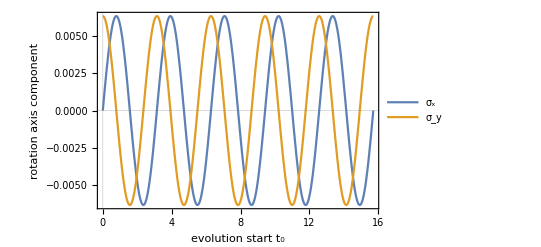

```mathematica
Plot[{RotAx[t][[1]],RotAx[t][[2]]},{t,0,tMax},Frame->{{True,False},{True,False}},FrameLabel->{"evolution start t_0","rotation axis component"},PlotLegends->{"σ_x","σ_y"},PlotRangePadding->{0,0.05},AxesOrigin->{0,0},GridLines->{{0},{0}}]
```